# 利用Wolfram语言进行视网膜图像分析

## 祝模芮 Southwest University

# #Wolfram Ambassador

## 引言

视网膜图像处理与分析是计算机视觉在医学领域的重要应用，视网膜的形态结构与人们的疾病如青光眼、糖尿病、高血压等其他眼底疾病关系密切，而通过医生进行人工进行眼底图像筛选的方式存在耗时、经验性太强等缺点，因此，利用计算机视觉技术根据眼底图像形态结构进行自动筛选将十分有意义。
	本次讲解的主要内容为：利用Wolfram语言强大的图像处理工具对视网膜眼底图像进行一系列预处理操作以及最终实现对视网膜血管的分割。

注：对图像的预处理操作主要参考汪维华博士论文《视网膜图像分割算法研究》
汪维华. 视网膜图像分割算法研究[D].中国科学院大学(中国科学院重庆绿色智能技术研究院),2018.

## 糖尿病发病率全球分布图

## -Graphics- -Graphics-

https : // diabetesatlas.org/en/

## Wolfram语言图像处理工具对视网膜图像预处理

### 原始眼底图像

原始视网膜图像组织目标与背景对比度低、光照不均、包含噪声多。需要对原始图像进行以下方式进行处理：

获取单通道颜色⟶  噪声滤波 ⟶ ROI提取 ⟶图像灰度倒置变换 ⟶ 光照均衡化⟶图像增强

```mathematica
笼屉
```

DRIVE数据集

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

https : // drive.grand - challenge.org/

### 获取单通道颜色

将原始图像分离为RGB三通道，其G（Green）通道中血管与背景的对比度最大，故选择G通道作为接下来的输入

```mathematica
ColorSeparate[-Graphics-]
```

{-Graphics-,-Graphics-,-Graphics-}

### 噪声滤波

利用高斯滤波器消除孤立点噪声，将r设置为2，即σ = 1,可避免模糊图像。

G(x,y)=1/(2 πσ^2)e(x^2+y^2)/(2 σ^2)

```mathematica
GaussianFilter[-Graphics-,2]
```

### 提取感兴趣区域（ROI）

#### 对图像进行二值化处理获得图像掩码

```mathematica
Binarize[-Graphics-,0.1]
```

-Graphics-

#### 将待处理图像与Imask相乘，得到ROI(感兴趣区域外所有像素值为0）

I_ROI=I_filter*I_mask

```mathematica
ImageMultiply[-Graphics-,-Graphics-]
```

-Graphics-

### 图像灰度倒置变换

```mathematica
ColorNegate[-Graphics-]
```

-Graphics-

### 光照均衡化

由于眼底相机在采集图像过程中光照不均一，同时视网膜各个部分对光线的吸收和反射率也不均匀，导致视网膜图像中的各个部分对比度不均匀，差别较大。
	为了消除光照对算法分割的影响，对视网膜图像采用光照均衡化方法。
	M:期望的平均像素值，对于8位灰度图像，我们直接取128
	窗口w内的平均像素值

(I_(eq(x,y) = I(x,y)+M-I))_w_mean(x,y)

```mathematica
BrightnessEqualize[-Graphics-]
```

-Graphics-

```mathematica
-Graphics-*-Graphics-
```

-Graphics-

获取未做均衡化处理的图像颜色直方图统计，可以看到图像光照不均匀现象较为明显

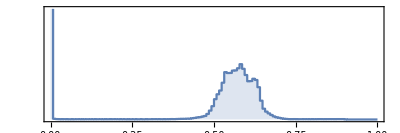

```mathematica
ImageHistogram[-Graphics-*-Graphics-]
```

获取结果颜色直方图统计，可以看到比均衡化之后的图像光照不均匀现象降低。

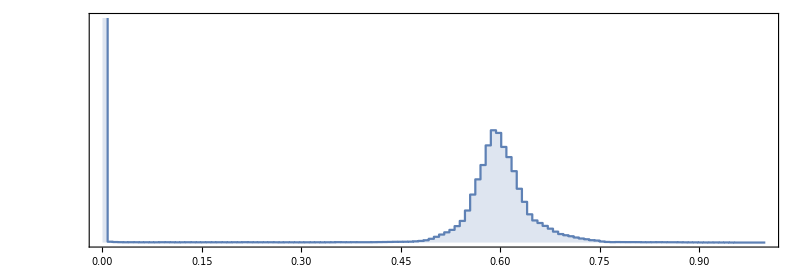

```mathematica
ImageHistogram[-Graphics-]
```

#### 图像增强(Super-Resolution)

```mathematica
SRNet=NetModel["Very Deep Net for Super-Resolution"]
```

NetChain[<>]

```mathematica
ImageResize[-Graphics-,{255,255}]
```

```mathematica
diff=Image[SRNet[-Graphics-]]
```

-Graphics-

```mathematica
diff+-Graphics-
```

-Graphics-

导入函数文件与图像源文件

```mathematica
<<"C:\\Users\\11309\\Desktop\\U_Net_Project\\UNet_Segmentation_My_Project\\UNET.m"; 
dirimg="C:\\Users\\11309\\Desktop\\U_Net_Project\\UNet_Segmentation_My_Project\\DRIVE_Datasets_training_tif\\training\\prepar_training_images"; 
dirmasks="C:\\Users\\11309\\Desktop\\U_Net_Project\\UNet_Segmentation_My_Project\\DRIVE_Datasets_training_tif\\training\\1st_manual";
<<"C:\\Users\\11309\\Desktop\\U_Net_Project\\UNet_Segmentation_My_Project\\UNET.m"; 
dirtestimg="C:\\Users\\11309\\Desktop\\U_Net_Project\\UNet_Segmentation_My_Project\\DRIVE_Datasets_training_tif\\test\\images_prepar"; 
dirtestmask="C:\\Users\\11309\\Desktop\\U_Net_Project\\UNet_Segmentation_My_Project\\DRIVE_Datasets_training_tif\\test\\annotion_hunman_1";
```

## Implementation of UNet - network for obtaining Vessels in Retinal images - in Wolfram Language:

### UNet-网络构架:

```mathematica
nNet=UNET
```

NetGraph[<>]

The Code based on :          https : // github.com/alihashmiii/UNet - Segmentation - Wolfram
The neural net architecture based on :     https : // lmb.informatik.uni - freiburg.de/people/ronneber/u - net/

### 读取训练集与测试集

```mathematica
{X,Y}=dataPrep[dirimg,dirmasks];
```

```mathematica
{testimages,testmasks}=dataPrep[dirtestimg,dirtestmask];
```

#### 训练集经过预处理后的图片

```mathematica
X
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 测试集经过预处理后的图片

```mathematica
testimages
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 模型训练

```mathematica
nNetInfo=trainNet[nNet,X[[;;20]],Y[[;;20]]]
```

NetTrain Results
summary | ,,  batches:80  rounds:20  time:13min  examples/s:0.52
data | ,,  training examples:20  processed examples:400  skipped examples:0
method | ,,  ADAMoptimizer  batch size5CPU
round | ,,  loss:3.07×10^-1  error:2.93%
 | 
 |

#### 模型损失随训练过程的变化

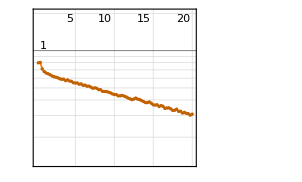
| rounds
loss | -Graphics-

```mathematica
nNetInfo["LossEvolutionPlot"]
```

#### 训练后的模型参数

```mathematica
nNetTrained=nNetInfo["TrainedNet"]
```

NetGraph[<>]

### 测试结果与标注图像对比

```mathematica
generateImage[]:=With[{imgs=Thread[{testimages[[1;;]],testmasks[[1;;]]}]},
MapAt[NetDecoder[{"Image"}],RandomChoice@imgs,2]
]
```

```mathematica
{img,ground}=generateImage[]
```

```mathematica
{img,#,ground,HighlightImage[img,MorphologicalPerimeter@Binarize@#]}&[NetDecoder[{"Image"}]@nNetTrained[img,TargetDevice-> "CPU"]]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

### 将训练后的模型权重文件储存到本地

```mathematica
saveNeuralNet[nNetTrained]
```

C:\Users\11309\Desktop\U_Net_Project\UNet_Segmentation_My_Project\unet.wlnet

### 导入训练后的模型

```mathematica
nNetTrained=Import["C:\\Users\\11309\\Desktop\\U_Net_Project\\UNet_Segmentation_My_Project\\unet.wlnet"]
```

NetGraph[<>]

### 对测试集图像进行批量测试

```mathematica
testdata = testimages[[1;;]];
```

```mathematica
res=NetDecoder[{"Image"}]@nNetTrained[testdata,TargetDevice-> "CPU"];
```

```mathematica
Rasterize@Grid[Partition[MapThread[Thumbnail[HighlightImage[#1,#2],100]&,{testdata,Map[DeleteSmallComponents@*Binarize]@res}],10]]
```

-Graphics-

```mathematica
IOU
```

## 感谢各位观看 欢迎大家批评指正！

本次演讲所引用内容在下方链接

预处理图像操作：汪维华. 视网膜图像分割算法研究[D].中国科学院大学 (中国科学院重庆绿色智能技术研究院), 2018.
https://diabetesatlas.org/en/
训练模型结构：      https : // github.com/alihashmiii/UNet - Segmentation - Wolfram
U-Net神经网络模型：   https : // lmb.informatik.uni - freiburg.de/people/ronneber/u - net/
Wolfram语言与系统-参考资料中心：  https://reference.wolfram.com/language/
Wolfram神经网络知识库:  https://resources.wolframcloud.com/NeuralNetRepository/
DRIVE数据集来源：https://drive.grand-challenge.org/